# NZFMR (Near Zero Field Magnetoresistance) of recombination current in Si:P Stochastic Liouville Equation (total spin basis)

```mathematica
Commute[A_,B_]:=A.B-B.A;AntiCommute[A_,B_]:=A.B+B.A
```

```mathematica
μB= 57.88*10^-9 (*eV/mT*);
ℏ= 6.582*10^-16(*eV s*);
g=2.003(* 2.003*);
```

S-T basis (Total Spin)

```mathematica
SLESolveS[a_, kS_, kD_,fudge_,range_List]:=

Module[{},


(* define spin operators*)
sz1=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, 1/2, 0}, {0, 0, 0, -1/2}});
sz2=({{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1/2, 0}, {0, 0, 0, -1/2}});
sx1=1/2({{0, 0, -1/√2, 1/√2}, {0, 0, 1/√2, 1/√2}, {-1/√2, 1/√2, 0, 0}, {1/√2, 1/√2, 0, 0}});
sy1=1/(2 ⅈ)({{0, 0, 1/√2, 1/√2}, {0, 0, -1/√2, 1/√2}, {-1/√2, 1/√2, 0, 0}, {-1/√2, -1/√2, 0, 0}});
sx2=1/2({{0, 0, 1/√2, -1/√2}, {0, 0, 1/√2, 1/√2}, {1/√2, 1/√2, 0, 0}, {-1/√2, 1/√2, 0, 0}});
sy2=1/(2 ⅈ)({{0, 0, -1/√2, -1/√2}, {0, 0, -1/√2, 1/√2}, {1/√2, 1/√2, 0, 0}, {1/√2, -1/√2, 0, 0}});
Sx1= KroneckerProduct[sx1,IdentityMatrix[2]];
Sx2= KroneckerProduct[sx2,IdentityMatrix[2]];
Sy1= KroneckerProduct[sy1,IdentityMatrix[2]];
Sy2= KroneckerProduct[sy2,IdentityMatrix[2]];
Sz1= KroneckerProduct[sz1,IdentityMatrix[2]];
Sz2= KroneckerProduct[sz2,IdentityMatrix[2]];

Ix=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[1]];Iy=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[2]];Iz=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[3]];

(* define singlet and triplet projection operators*)
Ps = DiagonalMatrix[Join[Table[1,{2^1}],Table[0,{4*2^1-2^1}]]];
Pt= DiagonalMatrix[Join[Table[0,{2^1}],Table[1,{4*2^1-2^1}]]];

dim=Dimensions[Ps]⟦1⟧;
equalGen=Table[1,{dim}];

Clear[ρ];
ρ=Table[ρME[i,j],{i,dim},{j,dim}];

(*Solve the SLE for the singlet part of the density matrix for each value of magnetic field Bx *)
ParallelTable[{Bz,fudge*Apply[#&,{(Tr[Ps.Evaluate[ρ/.Flatten[NSolve[(-I/ℏ Commute[g μB Bz * (Sz1 + Sz2 )  +g μB a (Ix.Sx1 + Iy.Sy1 + Iz.Sz1),ρ]-1/2 (kS+kD) AntiCommute[Ps,ρ]-1/2 kD AntiCommute[Pt,ρ])+1/dim DiagonalMatrix[equalGen]==0]//Chop]]])}]//Chop},{Bz,range⟦1⟧,range⟦2⟧,range⟦3⟧}]
]
```

Run the module:

```mathematica
testS = SLESolveS[1,4*10^6, 1*10^6,1,  {-10,10,0.02}];
```

Plot

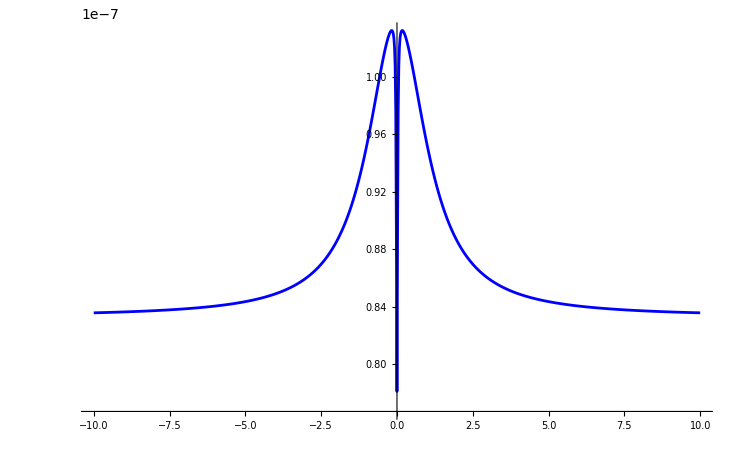

```mathematica
SLEplot1 = ListPlot[{testS}, Joined->True, PlotRange->All, PlotStyle->{{Blue},{Red}}]
```

Just to see what the singlet  and triplet projection operators looks like:

```mathematica
Ps//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Pt//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)